# NeRF: Neural Radiance Fields

```mathematica
$HistoryLength=0;
```

## Caméra 1D dans un monde 2D

```mathematica
unCarré[]:={{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}};
unCercle[]:=CirclePoints[32];
unTriangle[]:=CirclePoints[3];
```

```mathematica
Clear[place];
place[{posx_,posy_},angle_,{échellex_,échelley_}]:=TranslationTransform[{posx,posy}].RotationTransform[angle].ScalingTransform[{échellex,échelley}];
place[{posx_,posy_},angle_,échelle_]:=place[{posx,posy},angle,{échelle,échelle}];
place[{posx_,posy_},angle_]:=place[{posx,posy},angle,{1,1}];
place[{posx_,posy_}]:=place[{posx,posy},0,{1,1}];
```

```mathematica
see[e_]:={
If[KeyExistsQ[e,"couleur"],e[["couleur" ]],Black],If[KeyExistsQ[e,"densite"],Opacity[e[["densite"]]],Opacity[1]],
Polygon[e[["lignes" ]]]};

seeMonde[monde_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Block[{},(
Graphics[{
GrayLevel[0.8],Rectangle[{xmin,ymin},{xmax,ymax}],
GrayLevel[0.9],Thick,
Line[{{0,ymin},{0,ymax}}],
Line[{{xmin,0},{xmax,0}}],
see/@monde
}]
)]
```

```mathematica
e2p[v_]:=Append[v,1];
p2e[v_]:=Delete[v,-1]/v[[-1]];
```

```mathematica
seeCam[w2i_TransformationFunction,width_,depth_]:=Block[{i2w,coinsCam,coinsW},(
i2w=InverseFunction[w2i];
coinsCam={{0,1}*depth,{0,0},{width,1}*depth};
coinsW=i2w[coinsCam];
Graphics[{
PointSize[0.025],
Blue,Point[coinsW[[2]]],
Opacity[0.4],Polygon[coinsW]
}]
)]
```

## Prise de Photo 1D

```mathematica
Clear[render]
render[rgba_,δ_,fond_]:=Block[{σ,α,t},(
σ=rgba[[All,4]];
α=1-Exp[-σ δ];
t=Prepend[Exp[-Accumulate[σ δ]],1];
Total[rgba[[All,{1,2,3}]]*t[[1;;-2]]α]+t[[-1]]*fond
)]
```

```mathematica
photo[w2i_TransformationFunction,segment_]:=Block[{p,q,m},(
m=TransformationMatrix[w2i]; (* 3x3 avec  (0,0,1)  derniere  rangee *) 
p=(m.e2p[#])&/@segment;  (* (xh,zh,h) *) 
q=p/p[[All,2]]; (* (x/z,1,1/z) *) 
{#[[1]],1/#[[3]]}&/@q   (* (x/z,z) *)
)]
```

```mathematica
imageDataAlpha[img_Image,Missing[___]]:=ImageData[img];
imageDataAlpha[img_Image,densite_]:=Map[(#*{1.,1.,1.,densite})&,ImageData[img],{2}];
```

```mathematica
mix[clouds_]:=Block[{t},(
t=Max[Total[clouds[[All,4]]],10.^-6];
Append[Total[clouds[[All,1;;3]]*clouds[[All,4]]]/t,t]
)];
```

```mathematica
snapshot[w2i_TransformationFunction,monde_,width_,δ_,fond_]:=Block[{vg,zrange,ratio,nzx,nzxc,zxnc,zxc},(
vg={#[["couleur" ]],Polygon[photo[w2i,#[["lignes" ]]]]}&/@monde;
zrange=MinMax[Table[(List@@vg[[i,2]])[[1,All,2]],{i,1,Length[vg]}]];
zrange[[1]]=Max[0.1,zrange[[1]]]; (* distance minimale de la cam *) 
ratio=((zrange[[2]]-zrange[[1]])/width)/δ;
nzx=Rasterize[Graphics[{#},AspectRatio->ratio,PlotRange->{{0,width},zrange}],RasterSize->{width,Automatic},Background->None]&/@vg;
nzxc=MapThread[(imageDataAlpha[#1,#2])&,{nzx,monde[[All,"densite"]]}];
zxnc=Flatten[nzxc,{{2},{3},{1},{4}}];
zxc=Map[mix,zxnc,{2}];
Image[{render[#,δ,fond]&/@Transpose[zxc]},ImageSize->Scaled[0.9]]
)]
```

## Data

```mathematica
zap[w2i_,is_]:=<|"Input"->TransformationMatrix[InverseFunction[w2i]],"Target"->ImageData[is,Interleaving->False][[All,1]]|>
seeOut[o_]:=Image[{Transpose[o]},ImageSize->Scaled[1]]
```

### Create World

```mathematica
monde={
<|"couleur" ->Red,
"densite" ->0.4,
"lignes"->place[{0,1},0]@unCarré[]|>,
<|"couleur" ->Green,
"densite" ->0.4,
"lignes"->place[{-1,0},0]@unTriangle[]|>,
<|"couleur" ->Blue,
"densite" ->0.4,
"lignes"->place[{1,0},0]@unCercle[]|>
};
```

### Create Cameras

```mathematica
c2i=LinearFractionalTransform[({{50, 50, 0}, {0, 1, 0}, {0, 0, 1}})];
i2c=InverseFunction[c2i];
c2wS=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,0,360 Degree,2 Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@c2wS;
```

### See

```mathematica
Show[
seeMonde[monde,{{-5,5},{-5,5}}],
seeCam[#,100,0.9]&/@w2iS[[1;;-1;;8]]
]
```

-Graphics-

### Generate Data

```mathematica
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
```

```mathematica
data=MapThread[zap,{w2iS,is}];
data//Dimensions
data[[1,"Target"]]//Dimensions
```

{181}

{3,100}

### Train-Valid-Test Split

```mathematica
SeedRandom[1];
dataShuffled=RandomSample[data];
dataTrain=dataShuffled[[1;;-20]];
dataValid=dataShuffled[[-19;;-10]];
dataTest=dataShuffled[[-9;;-1]];
dataTrain//Dimensions
dataValid//Dimensions
dataTest//Dimensions
```

{162}

{10}

{9}

## NERF - Neural Network

```mathematica
(*equation 3 in https://arxiv.org/pdf/2003.08934*)
renderLayer[zStep_,n_,backgroundColor_]:=Block[{low,accumulate},(
low=LowerTriangularize[Table[1.,n,n]];
accumulate=NetGraph@FunctionLayer[Block[{rep,lower,times,acc},(
rep=ReplicateLayer[n]@#Input;
lower=NetArrayLayer["Array"->low,LearningRateMultipliers->0][];
times=ThreadingLayer[Times,None,InputPorts->{{n,n},{n,n}}][<|"Input1"->rep,"Input2"->lower|>];
acc=AggregationLayer[Total,2][times]
)]&];
NetGraph@FunctionLayer[Block[{density,alpha,transmitance,rgb,background,times,sum,out,value,transmitance2},(
density=#Input[[4]];
alpha=1-Exp[-density*zStep];
value=accumulate[density*zStep];
transmitance=Prepend[Exp[-value],1];
rgb=PartLayer[1;;3]@#Input;
background=transmitance[[-1]]*backgroundColor;
transmitance=PartLayer[1;;n][transmitance];
times=ThreadingLayer[Times,1,InputPorts->{{3,n},{n},{n}}][<|"Input1"->rgb,"Input2"->transmitance,"Input3"->alpha|>];
sum=AggregationLayer[Total,2][times];
out=ThreadingLayer[Plus,1,InputPorts->{{3},{3}}][<|"Input1"->sum,"Input2"->background|>];
out
)]&,"Input"->{4,n}]
)]
renderLayer[zStep_,n_]:=renderLayer[zStep,n,{0,0,0}]
```

```mathematica
camera2World[nbPixels_,zMin_,zMax_,zStep_]:=Block[{zRangeArray,xRangeArray},(
zRangeArray=NetArrayLayer["Array"->{Range[zMin,zMax,zStep]},LearningRateMultipliers->0];
xRangeArray=NetArrayLayer["Array"->{Range[0,100,100/(nbPixels-1)]},LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{a1,a2,b1,b2,i2wm,z,x,stepz,newz,ones,xp,onesp,onespp,grid,out},(
i2wm=#Input[[1;;2]];
a2=i2wm[[1,2]];
a1=i2wm[[1,1]];
b2=i2wm[[2,2]];
b1=i2wm[[2,1]];
z=zRangeArray[];
x=xRangeArray[];
stepz=Sqrt[(a2+ a1*x)^2+(b2+b1* x)^2];
newz=Transpose[stepz].(z*0+1);
ones=x*0+1;
xp=Transpose[x].z;
onesp=Transpose[ones].z;
onespp=onesp*0+1;
grid={xp/newz,onesp/newz,onespp};
out=i2wm.grid;
<|"Output"->out|>
)]&,"Input"->{3,3}]
)]
```

```mathematica
positionalEncodingLayer[L_]:=Block[{idxLayer},(
idxLayer=NetArrayLayer["Array"->Table[N[Pi]*2^i,{i,0,L-1}],LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{idx,x,y,xx,yy,xxx,yyy,xxxx,yyyy},(
x=FlattenLayer[{{2},{3},{1}}]@#Input[[1;;1]];
y=FlattenLayer[{{2},{3},{1}}]@#Input[[2;;2]];
idx=idxLayer[];
xx=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->x,"Input2"->idx|>];
yy=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->y,"Input2"->idx|>];
xxx={Sin[xx],Cos[xx]};
xxxx=FlattenLayer[{{1,4},{2},{3}}][xxx];
yyy={Sin[yy],Cos[yy]};
yyyy=FlattenLayer[{{1,4},{2},{3}}][yyy];
Join[xxxx,yyyy]
)]&,"Input"->{2,Automatic,Automatic}]
)]
```

```mathematica
Clear[nerfSampler];
nerfSampler[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayer[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]
```

```mathematica
trainableNet[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{nerf,lossLayer},(
nerf=nerfSampler[nbPixels,zMin,zMax,zStep,L];
lossLayer=MeanSquaredLossLayer[];

NetGraph@FunctionLayer[Block[{pred,loss},(
pred=nerf[#Input];
loss=lossLayer[<|"Input"->pred,"Target"->#Target|>];
<|"Output"->pred,"Loss"->loss|>
)]&,"Input"->{3,3},"Target"->{3,nbPixels}
]
)]
```

## Training

### Unit Test

```mathematica
tn=NetInitialize[trainableNet[100,1,8,0.1,5]]
```

NetGraph[…]

```mathematica
tn[dataTrain[[1]]]["Output"]//Dimensions
tn[dataTrain[[1]]]["Loss"]
seeOut@tn[dataTrain[[1]]]["Output"]
```

{3,100}

0.134116

-Graphics-

### Training Loop

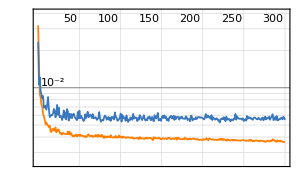
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12300  rounds:300  time:3.2min  examples/s:253
data | ,,  training examples:162  validation examples:10  processed examples:49200  skipped examples:0
method | ,,  ADAMoptimizer  batch size4  GPUAll
round | ,,  loss:3.67×10^-3
validation | ,,  loss:5.5×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=
NetTrain[
tn,
dataTrain,
All,
ValidationSet->dataValid,
BatchSize->4,
MaxTrainingRounds->300,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->{"GPU", All},
WorkingPrecision->"Real32"
]
```

```mathematica
Export["monModele.wlnet",tn]
```

monModele.wlnet

## Evaluation

```mathematica
quadRGBA[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->{a["rgba"],b["rgba"],d["rgba"],c["rgba"]}]
quadRGB[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->{a["rgb"],b["rgb"],d["rgb"],c["rgb"]}]
quadA[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->1-{a["a"],b["a"],d["a"],c["a"]}]
```

Retourne le plus d' information possible sur un pixel.
rgba : couleur rgb et alpha
rgb: couleur seulement
a: alpha seulement
p2d: point 2d dans le monde (x,y)

```mathematica
testFunction[net_,sample_]:=Block[{result,data},(
result=net[sample];
data=Join[result["rgba"],result["p2d"]];
data=Flatten[data,{{2},{3},{1}}];
Map[<|"rgba"->#[[1;;4]],"rgb"->#[[1;;3]],"a"->#[[4]],"p2d"->#[[5;;6]]|>&,data,{2}]
)]
```

### Unit Test

```mathematica
trained=netTrainResult["TrainedNet"]
```

NetGraph[…]

```mathematica
nb=3;
seeOut@dataTest[[nb,"Target"]]
seeOut@trained[dataTest[[nb]],TargetDevice->"CPU"]["Output"]
```

-Graphics-

-Graphics-

### Evaluate NERF

```mathematica
res=testFunction[trained,dataTest[[1]]];
res//Dimensions
```

{100,71}

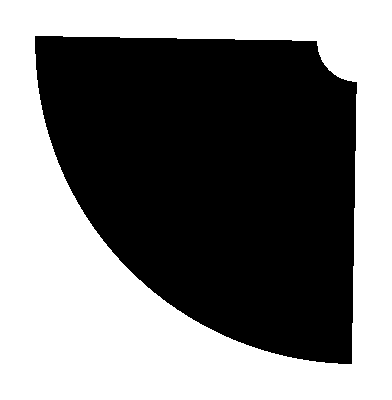

```mathematica
Graphics[{PointSize[0.01],Map[quadRGBA,Partition[res,{2,2},{1,1}],{2}]}]
```

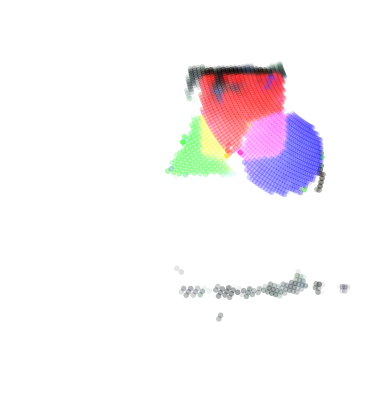

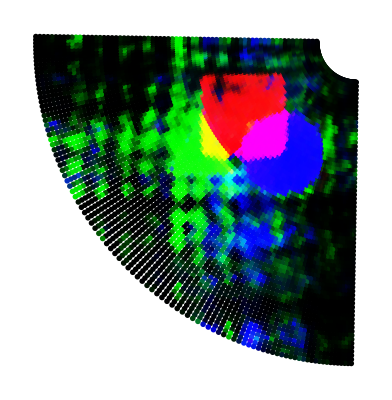

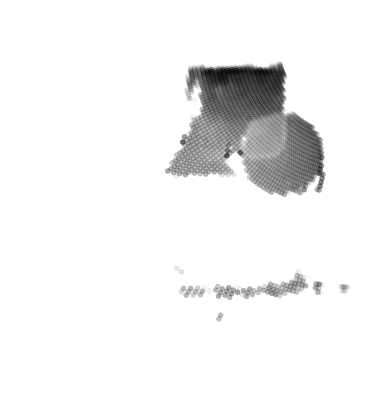

```mathematica
Graphics[{PointSize[0.01],Map[{RGBColor[#rgba],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{RGBColor[#rgb],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{GrayLevel[0,#a],Point[#p2d]}&,res,{2}]}]
```

## Un peu d'exploration

### Reconstruction

Le monde exemple contient un carre rouge, un triangle vert, et un rond bleu.

Faites d’autres mondes pour tester un peu plus le nerf.
1. Un monde avec plus d’ objets avec une bonne variation dans les densités. (utilisez des densités <=1)
2. Un monde qui est beaucoup plus difficile a reconstruire (a votre gout)
     Dans ce cas, on veut que le reseau apprennent bien les images (donc la loss descend tres bas) mais ne donne pas une bonne reconstruction.

```mathematica
(*Monde Exemple:Un carré rouge,un triangle vert,et un rond bleu*)
mondeExemple=Graphics[
{Style[Rectangle[{0,0},{1,1}],Red],
Style[Polygon[CirclePoints[{2,2},1,3]],Green],
Style[Disk[{4,0},0.5],Blue]},PlotRange->{{-1,5},{-1,3}},ImageSize->Medium
];
```

```mathematica
(*Monde avec plus d'objets avec des densités variées (densités<=1)*)
mondeVarie={
<|"couleur"->Red,
"densite"->0.4,
"lignes"->place[{0,1},0]@unCarré[]|>,
<|"couleur"->Green,
"densite"->0.3,
"lignes"->place[{-2,0},Pi/6]@unTriangle[]|>,
<|"couleur"->Blue,
"densite"->0.6,
"lignes"->place[{1,0},Pi/4]@unCercle[]|>,
<|"couleur"->Yellow,
"densite"->0.8,
"lignes"->place[{1,1},Pi/3]@unCarré[]|>,
<|"couleur"->Purple,
"densite"->0.5,"lignes"->place[{-1,-1},Pi/2]@unTriangle[]|>,
<|"couleur"->Orange,
"densite"->0.7,"lignes"->place[{0,-2},Pi/8]@unCercle[]|>};
```

```mathematica
(*Monde difficile à reconstruire*)mondeDifficile=Graphics[Table[Style[Polygon[CirclePoints[{RandomReal[{0,5}],RandomReal[{0,3}]},RandomReal[{0.2,1}],RandomInteger[{3,10}]]],Opacity[RandomReal[{0.2,0.8}]],RandomColor[]],{20}],PlotRange->{{-1,5},{-1,3}},ImageSize->Medium];
```

```mathematica
(*Afficher les mondes*)
Row[{mondeExemple,mondeVarie,mondeDifficile}]
```

```mathematica
Show[
seeMonde[mondeVarie,{{-5,5},{-5,5}}],
seeCam[#,100,0.9]&/@w2iS[[1;;-1;;8]]
]
```

-Graphics-

### Precision VS baseline

Faite une fonction qui calcule l’erreur moyenne du nerf sur un ensemble de test.
Faites un ensemble d’ entrainement avec un intervalle de s degres entre chaque camera (donc 0..360, step s)
Faites un ensemble de test avec un decallage k   (donc k...360 step s)

3. Faites un entrainement pour un step s=1, mais testez avec plusieurs (une dizaine) k,  entre k = 0 et k = s
     Affichez l' erreur moyenne obtenu pour differents k, et expliquez le resultats .

4. Refaites exactement la meme chose avec un S plus grand (par exemple 10). Expliquez le resultat.

Fonction pour calculer l’erreur moyenne

```mathematica
computeMeanError[net_,dataTest_]:=Module[
{results,losses,meanLoss},
results=net/@dataTest;
losses=results[[All,"Loss"]];
meanLoss=Mean[losses];
<|"Losses"->losses,"MeanLoss"->meanLoss|>]
```

Entraînement et test avec 𝑠=1 et différents 𝑘

```mathematica
s=1;
trainingAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,0,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@trainingAngles;
```

```mathematica
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTrain2=MapThread[zap,{w2iS,is}];
dataTrain2//Dimensions
dataTrain2[[1,"Target"]]//Dimensions
```

{361}

{3,100}

```mathematica
SeedRandom[1];
dataShuffled=RandomSample[dataTrain2];
splitIndex=Floor[0.8*Length[dataShuffled]];
dataTrain2=dataShuffled[[1;;splitIndex]];
dataValid2=dataShuffled[[splitIndex+1;;]];
dataTrain2//Dimensions
dataValid2//Dimensions
```

{288}

{73}

Test

```mathematica
k= 0;
testAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,k Degree,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@testAngles;
```

```mathematica
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTest21=MapThread[zap,{w2iS,is}];
dataTest21//Dimensions
dataTest21[[1,"Target"]]//Dimensions
```

{361}

{3,100}

```mathematica
k= 1;
testAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,k Degree,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@testAngles;
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTest22=MapThread[zap,{w2iS,is}];
dataTest22//Dimensions
dataTest22[[1,"Target"]]//Dimensions
```

{360}

{3,100}

Training

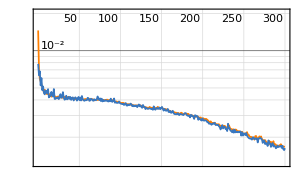
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:27300  rounds:300  time:9.2min  examples/s:197
data | ,,  training examples:361  validation examples:73  processed examples:109200  skipped examples:0
method | ,,  ADAMoptimizer  batch size4  GPUAll
round | ,,  loss:1.67×10^-3
validation | ,,  loss:1.63×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=
NetTrain[
tn,
dataTrain2,
All,
ValidationSet->dataValid2,
BatchSize->4,
MaxTrainingRounds->300,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->{"GPU", All},
WorkingPrecision->"Real32"
]
```

```mathematica
results= computeMeanError[tn, dataTest21];
losses1 = results["Losses"];
meanLoss1= results["MeanLoss"]
```

0.128776

```mathematica
results=tn/@dataTest21;
losses1=results[[All,"Loss"]];
meanLoss1=Mean[losses1]
```

0.128776

```mathematica
results= computeMeanError[tn, dataTest22];
losses2 = results["Losses"];
meanLoss2= results["MeanLoss"]
```

0.128795

```mathematica
ListPlot[
{losses1,losses2},
PlotStyle->{Red,Green},
PlotMarkers->{"●","▲"},
PlotLabel->"Pertes individuelles avec les moyennes",
Epilog->{{Blue,Thick,Line[{{1,meanLoss1},{Length[losses1],meanLoss1}}]},{Purple,Thick,Line[{{1,meanLoss2},{Length[losses2],meanLoss2}}]}},
PlotRange->All,
AxesLabel->{"Indice","Perte"},
PlotLegends->{"Pertes pour k=0","Pertes pour k=1"}
]
```

-Graphics-

Explications des resultats:
Le graphique montre les pertes individuelles pour deux configurations, k=0 (rouge) et k=1 (vert), tracées en fonction de l’indice, avec leurs moyennes respectives : une ligne bleue pour k=0 et une ligne violette pour k=1. Les pertes varient de manière similaire pour les deux configurations, augmentant au milieu des indices (100-250) et diminuant aux extrémités (1-50, 300-350).
La moyenne des pertes pour k=1 est légèrement inférieure à celle de k=0, ce qui suggère que la configuration k=1 produit de meilleures performances en minimisant davantage les pertes. Cependant, les différences sont faibles et pourraient nécessiter un test statistique pour confirmer leur significativité. Les résultats indiquent une forte corrélation entre les deux séries, suggérant que des facteurs communs influencent les pertes.

Entraînement et test avec 𝑠=10 et différents 𝑘

```mathematica
s=10;
trainingAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,0,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@trainingAngles;
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTrain3=MapThread[zap,{w2iS,is}];
dataTrain3//Dimensions
dataTrain3[[1,"Target"]]//Dimensions
SeedRandom[1];
dataShuffled=RandomSample[dataTrain3];
splitIndex=Floor[0.8*Length[dataShuffled]];
dataTrain3=dataShuffled[[1;;splitIndex]];
dataValid3=dataShuffled[[splitIndex+1;;]];
dataTrain3//Dimensions
dataValid3//Dimensions
```

{37}

{3,100}

{29}

{8}

```mathematica
k=0;
testAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,k Degree,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@testAngles;
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTest31=MapThread[zap,{w2iS,is}];
dataTest31//Dimensions
dataTest31[[1,"Target"]]//Dimensions
```

{37}

{3,100}

```mathematica
k=10;
testAngles=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,k Degree,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@testAngles;
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTest32=MapThread[zap,{w2iS,is}];
dataTest32//Dimensions
dataTest32[[1,"Target"]]//Dimensions
```

{36}

{3,100}

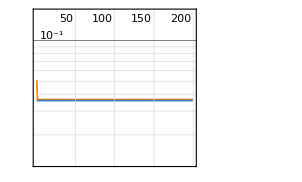
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1600  rounds:200  time:18min  examples/s:5.8
data | ,,  training examples:29  validation examples:8  processed examples:6400  skipped examples:0
method | ,,  ADAMoptimizer  batch size4CPU
round | ,,  loss:3.66×10^-2
validation | ,,  loss:3.6×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=
NetTrain[
tn,
dataTrain3,
All,
ValidationSet->dataValid3,
BatchSize->4,
MaxTrainingRounds->200,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->"CPU",
WorkingPrecision->"Real32"
]
```

```mathematica
results= computeMeanError[tn, dataTest31];
losses1 = results["Losses"];
meanLoss1= results["MeanLoss"]
```

0.128621

```mathematica
results= computeMeanError[tn, dataTest32];
losses2 = results["Losses"];
meanLoss2= results["MeanLoss"]
```

0.128809

```mathematica
ListPlot[
{losses1,losses2},
PlotStyle->{Red,Green},
PlotMarkers->{"●","▲"},
PlotLabel->"Pertes individuelles avec les moyennes",
Epilog->{{Blue,Thick,Line[{{1,meanLoss1},{Length[losses1],meanLoss1}}]},{Purple,Thick,Line[{{1,meanLoss2},{Length[losses2],meanLoss2}}]}},
PlotRange->All,
AxesLabel->{"Indice","Perte"},
PlotLegends->{"Pertes pour k=0","Pertes pour k=10"}
]
```

-Graphics-

Explications des resultats:
Ce graphique compare les pertes individuelles pour 𝑘=0 (points rouges) et 𝑘=10 (points verts), avec leurs moyennes respectives (lignes bleue et violette). Les deux séries présentent des variations similaires, avec des fluctuations marquées au milieu. Les moyennes des pertes sont proches, indiquant que 𝑘 a un impact limité sur les résultats globaux.
Cependant, les variations locales, comme les sommets au centre, suggèrent des différences spécifiques entre les deux configurations de 𝑘. Cela pourrait refléter une influence subtile, mais non négligeable, nécessitant une analyse statistique pour en évaluer l’importance.
Globalement, 𝑘=0 et 𝑘=10 semblent produire des résultats comparables, bien que certains indices montrent des pertes plus élevées ou plus basses. Une analyse approfondie des cas extrêmes et des fluctuations pourrait aider à optimiser 𝑘 pour minimiser les pertes et améliorer les performances globales.

### Ablation study

5. Changez l' architecture du reseau (les convolutions 128) pour autre chose et comparez les resultats.

6. Changez le “positional encoding” pour autre chose (une version plus simple, une plus complexe) et comparez les resultats.

7. Convertir un monde RGB en ton de gris (“ColorConvert[]”) et comparez le resultat de nerf sur les deux monde.

Changez l’ architecture du reseau (les convolutions 128) pour autre chose et comparez les resultats.

```mathematica
Clear[nerfSampler2];
nerfSampler2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayer[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]
```

```mathematica
trainableNet2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{nerf,lossLayer},(
nerf=nerfSampler2[nbPixels,zMin,zMax,zStep,L];
lossLayer=MeanSquaredLossLayer[];

NetGraph@FunctionLayer[Block[{pred,loss},(
pred=nerf[#Input];
loss=lossLayer[<|"Input"->pred,"Target"->#Target|>];
<|"Output"->pred,"Loss"->loss|>
)]&,"Input"->{3,3},"Target"->{3,nbPixels}
]
)]
```

```mathematica
tn=NetInitialize[trainableNet2[100,1,8,0.1,5]]
```

NetGraph[<2>, <7>]

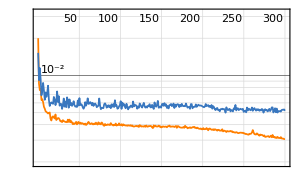
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12300  rounds:300  time:4.1min  examples/s:202
data | ,,  training examples:162  validation examples:10  processed examples:49200  skipped examples:0
method | ,,  ADAMoptimizer  batch size4  GPUAll
round | ,,  loss:3.06×10^-3
validation | ,,  loss:5.18×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=NetTrain[
tn,
dataTrain,
All,
ValidationSet->dataValid,
BatchSize->4,
MaxTrainingRounds->300,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->{"GPU", All},
WorkingPrecision->"Real32"
]
```

```mathematica
res=testFunction[trained,dataTest[[1]]];
res//Dimensions
```

{100,71}

```mathematica
Graphics[{PointSize[0.01],Map[quadRGBA,Partition[res,{2,2},{1,1}],{2}]}]
```

-Graphics-

```mathematica
Graphics[{PointSize[0.01],Map[{RGBColor[#rgba],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{RGBColor[#rgb],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{GrayLevel[0,#a],Point[#p2d]}&,res,{2}]}]
```

-Graphics-

-Graphics-

-Graphics-

Comparaison des resultats des convolutions 128 et 256
Perte sur l’ensemble d’entraînement :
- Convolution 128 : La perte diminue rapidement et se stabilise, mais reste légèrement plus élevée que pour la convolution 256.
- Convolution 256 : La perte est plus faible, indiquant un meilleur apprentissage, avec une meilleure stabilité.
Perte sur l’ensemble de validation :
- Convolution 128 : La courbe est stable avec un écart limité par rapport à l’ensemble d’entraînement, traduisant une bonne généralisation.
- Convolution 256 : Bien que stable, la perte est légèrement plus éloignée de celle de l’entraînement, suggérant un début d’overfitting.
Oscillations :
- Les oscillations sont légèrement réduites avec la convolution 256, traduisant une optimisation plus efficace.
Analyse globale :
- La convolution 256 améliore l’apprentissage sur l’ensemble d’entraînement grâce à une capacité accrue, mais cette augmentation se fait au détriment de la généralisation, avec un risque accru d’overfitting.
- La convolution 128 offre un meilleur compromis entre apprentissage et validation.

6. Changez le “positional encoding” pour autre chose (une version plus simple, une plus complexe) et comparez les resultats.

```mathematica
positionalEncodingLayerSimple[L_]:=Block[{idxLayer},(
idxLayer=NetArrayLayer["Array"->Table[N[Pi],{i,0,L-1}],LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{idx,x,y,xx,yy,xxx,yyy,xxxx,yyyy},(
x=FlattenLayer[{{2},{3},{1}}]@#Input[[1;;1]];
y=FlattenLayer[{{2},{3},{1}}]@#Input[[2;;2]];
idx=idxLayer[];
xx=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->x,"Input2"->idx|>];
yy=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->y,"Input2"->idx|>];
xxx={xx,xx};
xxxx=FlattenLayer[{{1,4},{2},{3}}][xxx];
yyy={yy,yy};
yyyy=FlattenLayer[{{1,4},{2},{3}}][yyy];
Join[xxxx,yyyy]
)]&,"Input"->{2,Automatic,Automatic}]
)]
```

```mathematica
positionalEncodingLayerComplex[L_]:=Block[{idxLayer},(
idxLayer=NetArrayLayer["Array"->Table[N[Pi]*Sqrt[2^i],{i,0,L-1}],LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{idx,x,y,xx,yy,xxx,yyy,xxxx,yyyy},(
x=FlattenLayer[{{2},{3},{1}}]@#Input[[1;;1]];
y=FlattenLayer[{{2},{3},{1}}]@#Input[[2;;2]];
idx=idxLayer[];
xx=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->x,"Input2"->idx|>];
yy=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->y,"Input2"->idx|>];
xxx={Sin[xx]*Cos[xx],Cos[xx]*Sin[xx]};
xxxx=FlattenLayer[{{1,4},{2},{3}}][xxx];
yyy={Sin[yy]*Cos[yy],Cos[yy]*Sin[yy]};
yyyy=FlattenLayer[{{1,4},{2},{3}}][yyy];
Join[xxxx,yyyy]
)]&,"Input"->{2,Automatic,Automatic}]
)]
```

Pour “positional encoding” simple.

```mathematica
Clear[nerfSampler2];
nerfSampler2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayerSimple[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]
```

```mathematica
trainableNet2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{nerf,lossLayer},(
nerf=nerfSampler2[nbPixels,zMin,zMax,zStep,L];
lossLayer=MeanSquaredLossLayer[];

NetGraph@FunctionLayer[Block[{pred,loss},(
pred=nerf[#Input];
loss=lossLayer[<|"Input"->pred,"Target"->#Target|>];
<|"Output"->pred,"Loss"->loss|>
)]&,"Input"->{3,3},"Target"->{3,nbPixels}
]
)]
```

```mathematica
tn=NetInitialize[trainableNet2[100,1,8,0.1,5]]
```

NetGraph[<2>, <7>]

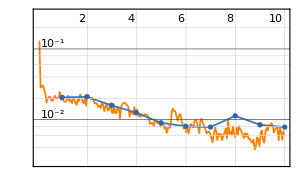
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:410  rounds:10  time:13min  examples/s:2.2
data | ,,  training examples:162  validation examples:10  processed examples:1640  skipped examples:0
method | ,,  ADAMoptimizer  batch size4CPU
round | ,,  loss:6.91×10^-3
validation | ,,  loss:7.82×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=NetTrain[
tn,
dataTrain,
All,
ValidationSet->dataValid,
BatchSize->4,
MaxTrainingRounds->10,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->"CPU",
WorkingPrecision->"Real32"
]
```

Pour “positional encoding”  complexe.

```mathematica
Clear[nerfSampler2];
nerfSampler2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayerComplex[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[256,{1,1}],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]
```

```mathematica
trainableNet2[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{nerf,lossLayer},(
nerf=nerfSampler2[nbPixels,zMin,zMax,zStep,L];
lossLayer=MeanSquaredLossLayer[];

NetGraph@FunctionLayer[Block[{pred,loss},(
pred=nerf[#Input];
loss=lossLayer[<|"Input"->pred,"Target"->#Target|>];
<|"Output"->pred,"Loss"->loss|>
)]&,"Input"->{3,3},"Target"->{3,nbPixels}
]
)]
```

```mathematica
tn=NetInitialize[trainableNet2[100,1,8,0.1,5]]
```

NetGraph[<2>, <7>]

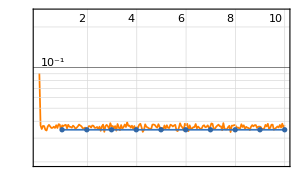
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:410  rounds:10  time:12min  examples/s:2.4
data | ,,  training examples:162  validation examples:10  processed examples:1640  skipped examples:0
method | ,,  ADAMoptimizer  batch size4CPU
round | ,,  loss:3.64×10^-2
validation | ,,  loss:3.46×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=NetTrain[
tn,
dataTrain,
All,
ValidationSet->dataValid,
BatchSize->4,
MaxTrainingRounds->10,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->"CPU",
WorkingPrecision->"Real32"
]
```

### Dernier detail

Vous avez remarqué que le “positional encoding” est seulement calcule sur x et y, mais pas sur la direction (voir l’article NERF).
8. A votre avis, quel est l’impact de cette omision? (Autrement dit, a quoi sert la direction? Dans quel cas est-ce que la direction est vraiment utile pour NERF?)

Dans NeRF, l’encodage directionnel est crucial pour générer des rendus réalistes, car il capture l’interaction entre la lumière et les surfaces en fonction de l’angle de vue. La direction de la caméra influence des effets comme les réflexions, les ombres, ... Omettre la direction dans notre modèle peut nuire à la génération de nouvelles vues réalistes, rendre les objets plats, et limiter l’apprentissage de la scène 3D, notamment pour des matériaux réfléchissants ou transparents. En somme, la direction est essentielle pour simuler correctement les interactions lumineuses et obtenir des rendus photoréalistes.